# Chapter 2

## Setup

```mathematica
Unprotect[DivisorSigma];

DivisorSigma[m_Integer]:=DivisorSigma[1,m];
SyntaxInformation[DivisorSigma]={"ArgumentsPattern"->{_,_.}};
Format[HoldPattern[DivisorSigma[m_]],TraditionalForm]:=
σ[m];

Protect[DivisorSigma];
```

```mathematica
Attributes[DivisorTau]=Listable;

DivisorTau[n_Integer]:=
DivisorSigma[0,n];

Format[DivisorTau,TraditionalForm]=τ;
```

```mathematica
Attributes[DivisorS]=Listable;
DivisorS[n_Integer?Positive]:=
DivisorSigma[n]-n;

Format[DivisorS,TraditionalForm]=s;
```

```mathematica
PerfectNumberQ[n_]:=
DivisorS[n]===n;
```

```mathematica
factorsDivisorD[n_Integer]:=
Tuples[
Replace[
MapAt[IntegerPartitions,FactorInteger@n,{All,-1}],
{p_Integer,parts_List}:>
Map[p^#-1&,parts],
{1}]];

DivisorD[n_Integer]:=
With[{factors=FactorInteger[n]},
Min[
Apply[Times]@*(Prime[Range@Length@#]^Reverse@Sort@#&)@*Flatten/@
factorsDivisorD[n]]];

Format[DivisorD,TraditionalForm]=D;
```

```mathematica
MultiplicationTable[xs_List,ys_List,op_:Times]:=
TableForm[Outer[op,xs,ys],TableHeadings->{xs,ys}];
```

## Section 2.1

### Exercise 2.1.1

```mathematica
?*set*Q
```

RowBox[{"SubsetQ", "[", RowBox[{SubscriptBox[StyleBox["list", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["2", "TR"]]}], "]"}] yields True if SubscriptBox[StyleBox["list", "TI"], StyleBox["2", "TR"]] is a subset of SubscriptBox[StyleBox["list", "TI"], StyleBox["1", "TR"]], and False otherwise.

```mathematica
With[{facts=FactorInteger[60]/.{p_Integer,k_Integer}:>p^Range[0,k]},
Sort@Flatten[Outer[Times,Sequence@@facts]]==Divisors[60]]
```

True

```mathematica
Apply[
Times,
FactorInteger[60]/.{p_?PrimeQ,k_Integer?Positive}:>
k+1]
```

12

```mathematica
Sum[1,{d,Divisors[60]}]
```

12

```mathematica
?DivisorSigma
```

RowBox[{"DivisorSigma", "[", RowBox[{StyleBox["k", "TI"], ",", StyleBox["n", "TI"]}], "]"}] gives the divisor function RowBox[{SubscriptBox["σ", StyleBox["k", "TI"]], "(", StyleBox["n", "TI"], ")"}].

```mathematica
DivisorSigma[1,60]
```

168

### Exercise 2.1.2

```mathematica
Table[Sum[1,{d,Divisors[n]}],{n,2^Range[4]}]
```

{2,3,4,5}

```mathematica
Table[Sum[1,{d,Divisors[n]}],{n,3^Range[4]}]
```

{2,3,4,5}

```mathematica
Table[Sum[1,{d,Divisors[n]}],{n,5^Range[4]}]
```

{2,3,4,5}

For  n==p^k, where p ∈ ℙ, τ(n)==k+1.

```mathematica
DivisorSigma[1,2^Range[4]]
```

{3,7,15,31}

```mathematica
DivisorSigma[1,3^Range[4]]
```

{4,13,40,121}

```mathematica
DivisorSigma[1,5^Range[4]]
```

{6,31,156,781}

For n==p^k,

1n==∑_(m=0)^k p^m==(1-p^(k+1))/(1-p)

```mathematica
(1-p^(k+1))/(1-p)/.p->2/.k->{1,2,3,4}
```

{3,7,15,31}

```mathematica
(1-p^(k+1))/(1-p)/.p->3/.k->{1,2,3,4}
```

{4,13,40,121}

```mathematica
(1-p^(k+1))/(1-p)/.p->5/.k->{1,2,3,4}
```

{6,31,156,781}

### Exercise 2.1.3

```mathematica
{DivisorTau[3],DivisorTau[2],DivisorTau[6]}
```

{2,2,4}

```mathematica
{DivisorTau[6],DivisorTau[35],DivisorTau[6*35]}
```

{4,4,16}

```mathematica
{DivisorTau[6],DivisorTau[4],DivisorTau[6*4]}
```

{4,3,8}

For {m,n}⊂ℤ ∧gcd(m,n)==1, τ(m) τ(n)==τ(m n).

### Exercise 2.1.4

```mathematica
{DivisorSigma[1,3],DivisorSigma[1,2],DivisorSigma[1,3*2]}
```

{4,3,12}

```mathematica
{DivisorSigma[1,6],DivisorSigma[1,35],DivisorSigma[1,6*35]}
```

{12,48,576}

```mathematica
%[[1]]*%[[2]]
```

576

```mathematica
{DivisorSigma[6],DivisorSigma[35],DivisorSigma[6*35]}
```

{12,48,576}

```mathematica
{DivisorSigma[6],DivisorSigma[4],DivisorSigma[6*4]}
```

{12,7,60}

For {m,n}⊂ℤ ∧gcd(m,n)==1, σ(m) σ(n)==σ(m n).

### Exercise 2.1.5

#### τ(n)

```mathematica
DivisorTau/@(2^Range[5])
```

{2,3,4,5,6}

If a number n has prime factorization p_1^k_1 p_2^k_2 p_m^k_m, then

τ(n)==∑_(j=1)^m (k_j+1)

#### σ(n)

```mathematica
DivisorSigma/@(2^Range[5])
```

{3,7,15,31,63}

```mathematica
2^(Range[5]+1)-1
```

{3,7,15,31,63}

If a number n has prime factorization p_1^k_1 p_2^k_2 p_m^k_m, then

σ(n)==∑_(j=1)^m (p_j^(k_j+1)-1)/(p_j-1)

```mathematica
DivisorSigma[36]
```

91

```mathematica
(2^3-1)/(2-1)×(3^3-1)/(3-1)
```

91

### Exercise 2.1.6

```mathematica
DivisorS[36]
```

55

```mathematica
DivisorS[4]
```

3

```mathematica
DivisorS[9]
```

4

```mathematica
DivisorS[4]*DivisorS[9]+4*DivisorS[9]+DivisorS[4]*9
```

55

gcd(m,n)==1⇒s(m n)==n s(m)+s(m) s(n)+m s(n)

### Exercise 2.1.7

```mathematica
PerfectNumberQ[2^1×3]
```

True

```mathematica
PerfectNumberQ[2^2×7]
```

True

```mathematica
Through[{Total,Identity}[Most@Divisors[8128]]]
```

{8128,{1,2,4,8,16,32,64,127,254,508,1016,2032,4064}}

```mathematica
PrimeQ[127]
```

True

Conjecture that 2^(p-1)×(2^p-1)is a perfect number when p∈ℙ and 2^p-1∈ℙ.

### Exercise 2.1.8

#### 1.

```mathematica
n=130816
```

130816

```mathematica
n==2^8*(2^9-1)
```

True

```mathematica
FactorInteger[n]
```

{{2,8},{7,1},{73,1}}

```mathematica
%/.{p_,k_}:>(p^(k+1)-1)/(p-1)
```

{511,8,74}

```mathematica
Apply[Times,%]
```

302512

```mathematica
%-n
```

171696

```mathematica
%==n
```

False

#### 2.

```mathematica
n=2^10*(2^11-1)
```

2096128

```mathematica
FactorInteger[n]/.{p_,k_}:>(p^(k+1)-1)/(p-1)
```

{2047,24,90}

```mathematica
(Times@@%)-n
```

2325392

#### 3.

```mathematica
p=13;
```

```mathematica
n=2^(p-1)*(2^p-1)
```

33550336

```mathematica
factors=FactorInteger@n
```

{{2,12},{8191,1}}

```mathematica
(#1^(#2+1)-1)/(#1-1)&@@@factors
```

{8191,8192}

```mathematica
Times@@%
```

67100672

```mathematica
%-n
```

33550336

### Exercise 2.1.9

```mathematica
n=2^77-1
```

151115727451828646838271

```mathematica
q=2^7-1
```

127

```mathematica
?Divisible
```

Divisible[n,m] yields True if n is divisible by m, and yields False if it is not.

```mathematica
Divisible[n,q]
```

True

```mathematica
r=2^11-1
```

2047

```mathematica
Divisible[n,r]
```

True

```mathematica
r*q
```

259969

```mathematica
n/r/q
```

581283643249112959

```mathematica
FactorInteger[%]
```

{{581283643249112959,1}}

### Exercise 2.1.10

```mathematica
Mersenne[n_Integer?Positive]:=2^Prime[n]-1;
```

```mathematica
Select[
AssociationThread[Prime/@Range[10],Mersenne/@Range[10]],
PrimeQ]
```

<|2→3,3→7,5→31,7→127,13→8191,17→131071,19→524287|>

```mathematica
2^16*(2^17-1)
```

8589869056

```mathematica
PerfectNumberQ@%
```

True

### Exercise 2.1.11

n==2^(p-1) (2^p-1)

σ(n)==σ(2^(p-1)) σ(2^p-1)

σ(2^(p-1))==(2^p-1)/(2-1)

σ(2^p-1)==(2^p-1)+1==2 2^(p-1)

σ(n)==2 (2^p-1) 2^(p-1)==2 n

### Exercise 2.1.12

```mathematica
2^2 7
```

28

```mathematica
28==1^3+3^3
```

True

```mathematica
2^4 31
```

496

```mathematica
1^3+3^3+5^3+7^3
```

496

```mathematica
2^6 127
```

8128

```mathematica
(2*Range[1,8]-1)^3
```

{1,27,125,343,729,1331,2197,3375}

```mathematica
Total[%]
```

8128

Conjecture that for p∈ℙ, p odd,

∑_(k=1)^(p-1) (2 k-1)^3==2^(p-1) (2^p-1)

### Exercise 2.1.13

```mathematica
Sum[k^3,{k,1,2*n}]
```

n^2 (1+2 n)^2

```mathematica
Sum[(2*k)^3,{k,1,n}]==2*n^2(1+n)^2
```

True

```mathematica
Sum[k^3,{k,1,2*n}]-Sum[(2*k)^3,{k,1,n}]
```

-2 n^2 (1+n)^2+n^2 (1+2 n)^2

```mathematica
Simplify[%]
```

n^2 (-1+2 n^2)

```mathematica
%/.n->2^((p-1)/2)
```

2^(-1+p) (-1+2^p)

### Exercise 2.1.14

```mathematica
AssociationMap[DivisorS,Range[10]]
```

<|1→0,2→1,3→1,4→3,5→1,6→6,7→1,8→7,9→4,10→8|>

```mathematica
Map[OddQ,%]
```

<|1→False,2→True,3→True,4→True,5→True,6→False,7→True,8→True,9→False,10→False|>

```mathematica
DivisorS[Prime[Range[10]]^4]
```

{15,40,156,400,1464,2380,5220,7240,12720,25260}

For n==p^k, for p∈ℙ, and p odd, then s(n) is odd if k is even. s(2^k) is even when k is even.

Using the known relationship for σ(m n) where gcd(m,n)==1, we have

s(m n)==-n σ(m)+σ(m) σ(n)-m σ(n)

```mathematica
With[{primes=Prime[Range[10]],powers=Range[4]},
TableForm[
Map[DivisorS,Transpose@Outer[Power,primes,powers]],
TableAlignments->Right,
TableHeadings->{p^powers,primes}
]]//TraditionalForm
```

| 2 | 3 | 5 | 7 | 11 | 13 | 17 | 19 | 23 | 29
p | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
p^2 | 3 | 4 | 6 | 8 | 12 | 14 | 18 | 20 | 24 | 30
p^3 | 7 | 13 | 31 | 57 | 133 | 183 | 307 | 381 | 553 | 871
p^4 | 15 | 40 | 156 | 400 | 1464 | 2380 | 5220 | 7240 | 12720 | 25260

For p∈ℙ, we have σ(p^k)==(p^(k+1)-1)/(p-1). For p==2, this is always odd. For p odd, both numerator and denominator are even independent of k.

σ(p^k)-σ(p^(k-1))==p^k

The difference is always odd, so σ(p^k) always has different parity from σ(p^(k-1)). This explains both the behavior of σ(p^k) and s(p^k).

Because s(n)==σ(n)-n, then we have

```mathematica
With[{result=If[Not@Xor[##],HoldForm[EvenQ[DivisorS[n]]],HoldForm[OddQ[DivisorS[n]]]]},
HoldForm[Implies[
EvenQ[n]==#1&&EvenQ[DivisorSigma[n]]==#2,
result
]]]&@@@Tuples[{True,False},2]//Column//TraditionalForm
```

EvenQ[n]==True∧EvenQ[σ(n)]==True⇒EvenQ[s(n)]
EvenQ[n]==True∧EvenQ[σ(n)]==False⇒OddQ[s(n)]
EvenQ[n]==False∧EvenQ[σ(n)]==True⇒OddQ[s(n)]
EvenQ[n]==False∧EvenQ[σ(n)]==False⇒EvenQ[s(n)]

From the previous formula for σ(n), if n==2^k p_1^k_1…  p_2^k_2 p_n^k_n, for the p_jbeing odd primes, then σ(n) is even if any of the k_j are even. Thus s(n) is even if k==0 and all the k_j are odd, or if 1≤k and at least one of the k_j is even.

### Exercise 2.1.15

```mathematica
{{m=284,Apply[Times,HoldForm[#1^#2]&@@@ FactorInteger[m]]},
{n=220,Apply[Times,HoldForm[#1^#2]&@@@ FactorInteger[n]]}}//TableForm
```

284 | 2^2 71^1
220 | 2^2 5^1 11^1

```mathematica
DivisorS[284]
```

220

```mathematica
DivisorS[220]
```

284

```mathematica
{#,FactorInteger[#],DivisorS[#]}&[16]
```

{16,{{2,4}},15}

```mathematica
DivisorSigma[71]
```

72

```mathematica
DivisorSigma[5]
```

6

```mathematica
DivisorSigma[11]
```

12

```mathematica
DivisorS[71]
```

1

```mathematica
DivisorS[55]
```

17

```mathematica
2*71
```

142

```mathematica
DivisorS[2*71]
```

74

```mathematica
DivisorS[2*55]
```

106

```mathematica
primes=Prime@Range[2,100]
```

{3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541}

```mathematica
DivisorSigma[primes]
```

{4,6,8,12,14,18,20,24,30,32,38,42,44,48,54,60,62,68,72,74,80,84,90,98,102,104,108,110,114,128,132,138,140,150,152,158,164,168,174,180,182,192,194,198,200,212,224,228,230,234,240,242,252,258,264,270,272,278,282,284,294,308,312,314,318,332,338,348,350,354,360,368,374,380,384,390,398,402,410,420,422,432,434,440,444,450,458,462,464,468,480,488,492,500,504,510,522,524,542}

```mathematica
prods=AssociationMap[Reverse]@AssociationMap[
Apply[Times]@*Map[DivisorSigma],
Tuples[primes,2]];
```

```mathematica
lim=NextPrime[Keys[prods][[-1]],-1]
```

293749

```mathematica
morePrimes=Prime[Range[2,PrimePi[lim]]];
```

```mathematica
morePrimes[[-1]]
```

293749

```mathematica
prods[lim]
```

Missing[KeyAbsent,293749]

```mathematica
TakeWhile[prods,#≤71&]
```

<||>

```mathematica
relations=Select[AssociationMap[prods@*(#+1&),morePrimes],Not@*MissingQ];
```

```mathematica
Take[relations,1]
```

<|23→{5,3}|>

```mathematica
DivisorSigma[23]==DivisorSigma[5*3]
```

True

```mathematica
DivisorS[5*3]
```

9

```mathematica
Array[Prepend[{3,5},2^#-1]&,5]
```

{{1,3,5},{3,3,5},{7,3,5},{15,3,5},{31,3,5}}

```mathematica
DivisorSigma[4]
```

7

```mathematica
7*72-4*71
```

220

```mathematica
7*72-4*5*11
```

284

```mathematica
71-55
```

16

```mathematica
DivisorSigma[32]
```

63

```mathematica
32*15
```

480

```mathematica
32*23
```

736

```mathematica
31*24-16*15
```

504

```mathematica
31*24-16*23
```

376

```mathematica
24*48
```

1152

```mathematica
1151+1
```

1152

### Exercise 2.1.16

If s(m)==n and s(n)==m, then we have

σ(m)==s(m)+m==m+n

and

σ(n)==s(n)+n==m+n

### Generating pairs

```mathematica
col[1]=2^Range[20]
```

{2,4,8,16,32,64,128,256,512,1024,2048,4096,8192,16384,32768,65536,131072,262144,524288,1048576}

```mathematica
col[2]=col[1]*3
```

{6,12,24,48,96,192,384,768,1536,3072,6144,12288,24576,49152,98304,196608,393216,786432,1572864,3145728}

```mathematica
col[3]=col[2]-1
```

{5,11,23,47,95,191,383,767,1535,3071,6143,12287,24575,49151,98303,196607,393215,786431,1572863,3145727}

```mathematica
col[4]=(#1*#2-1&)@@@Partition[col[2],2,1]
```

{71,287,1151,4607,18431,73727,294911,1179647,4718591,18874367,75497471,301989887,1207959551,4831838207,19327352831,77309411327,309237645311,1236950581247,4947802324991}

```mathematica
TableForm[MapThread[
Join,
{Transpose[Array[col,2]],
Transpose[PadLeft[Array[col,3,2],{2,Length@col[1]},""]]/.n_Integer/;!PrimeQ[n]:>""
}],
TableAlignments->Right]
```

2 | 6 | 5 | 
4 | 12 | 11 | 71
8 | 24 | 23 | 
16 | 48 | 47 | 1151
32 | 96 |  | 
64 | 192 | 191 | 
128 | 384 | 383 | 73727
256 | 768 |  | 294911
512 | 1536 |  | 
1024 | 3072 |  | 
2048 | 6144 | 6143 | 18874367
4096 | 12288 |  | 
8192 | 24576 |  | 
16384 | 49152 |  | 
32768 | 98304 |  | 
65536 | 196608 |  | 
131072 | 393216 |  | 
262144 | 786432 | 786431 | 
524288 | 1572864 |  | 
1048576 | 3145728 |  |

### Exercise 2.1.17

σ(2^k p q)==σ(2^k) σ(p) σ(q)

σ(2^k)==2^(k+1)-1

σ(p)==p+1

σ(q)==q+1

σ(2^k p q)==(2^(k+1)-1) (p+1) (q+1)

```mathematica
rhs=(2^(k+1)-1)*(p+1)*(q+1)
```

(-1+2^(1+k)) (1+p) (1+q)

```mathematica
simplified=Simplify[Expand[rhs]/.{p->3*2^(k-1)-1,q->3*2^k-1}]
```

9 2^(-1+2 k) (-1+2^(1+k))

```mathematica
simplified/.(9*2^(2k-1))->(r+1)
```

(-1+2^(1+k)) (1+r)

σ(2^k r)==σ(2^k) σ(r)==(2^k-1) (r+1)

### Exercise 2.1.18

```mathematica
eqns={p==3*2^(k-1)-1,q==3*2^k-1,r==9*2^(2k-1)-1}
```

{p==-1+3 2^(-1+k),q==-1+3 2^k,r==-1+9 2^(-1+2 k)}

```mathematica
Style[TraditionalForm[Column@eqns],"DisplayFormula"]
```

p==3 2^(k-1)-1
q==3 2^k-1
r==9 2^(2 k-1)-1

```mathematica
{Expand[(2*p+1/.Rule@@eqns[[1]])],eqns[[2]]}
```

{-1+3 2^k,q==-1+3 2^k}

```mathematica
Expand[2*p^2+4*p+1/.Rule@@eqns[[1]]]==eqns[[-1,-1]]
```

True

### Exercise 2.1.19 and 2.1.20

```mathematica
With[{n=RandomInteger[{1,300}]},
NestWhileList[DivisorS,n,Positive]]
```

{174,186,198,270,450,759,393,135,105,87,33,15,9,4,3,1,0}

```mathematica
NestList[DivisorS,276,10]
```

{276,396,696,1104,1872,3770,3790,3050,2716,2772,5964}

```mathematica
FactorInteger[276]
```

{{2,2},{3,1},{23,1}}

```mathematica
ss=
AssociationMap[
NestWhileList[DivisorS,Echo@#,With[{xs={##}},Last@xs≠0&&!MemberQ[Most@xs,Last@xs]]&,{2,Infinity}]&,
DeleteCases[Range[300],276]];
```

```mathematica
Map[Last,ss]
```

<|1→0,2→0,3→0,4→0,5→0,6→6,7→0,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0,16→0,17→0,18→0,19→0,20→0,21→0,22→0,23→0,24→0,25→6,26→0,27→0,28→28,29→0,30→0,31→0,32→0,33→0,34→0,35→0,36→0,37→0,38→0,39→0,40→0,41→0,42→0,43→0,44→0,45→0,46→0,47→0,48→0,49→0,50→0,51→0,52→0,53→0,54→0,55→0,56→0,57→0,58→0,59→0,60→0,61→0,62→0,63→0,64→0,65→0,66→0,67→0,68→0,69→0,70→0,71→0,72→0,73→0,74→0,75→0,76→0,77→0,78→0,79→0,80→0,81→0,82→0,83→0,84→0,85→0,86→0,87→0,88→0,89→0,90→0,91→0,92→0,93→0,94→0,95→6,96→0,97→0,98→0,99→0,100→0,101→0,102→0,103→0,104→0,105→0,106→0,107→0,108→0,109→0,110→0,111→0,112→0,113→0,114→0,115→0,116→0,117→0,118→0,119→6,120→0,121→0,122→0,123→0,124→0,125→0,126→0,127→0,128→0,129→0,130→0,131→0,132→0,133→0,134→0,135→0,136→0,137→0,138→0,139→0,140→0,141→0,142→0,143→6,144→0,145→0,146→0,147→0,148→0,149→0,150→0,151→0,152→0,153→0,154→0,155→0,156→0,157→0,158→0,159→0,160→0,161→0,162→0,163→0,164→0,165→0,166→0,167→0,168→0,169→0,170→0,171→0,172→0,173→0,174→0,175→0,176→0,177→0,178→0,179→0,180→0,181→0,182→0,183→0,184→0,185→0,186→0,187→0,188→0,189→0,190→0,191→0,192→0,193→0,194→0,195→0,196→0,197→0,198→0,199→0,200→0,201→0,202→0,203→0,204→0,205→0,206→0,207→0,208→0,209→0,210→0,211→0,212→0,213→0,214→0,215→0,216→0,217→0,218→0,219→0,220→220,221→0,222→0,223→0,224→0,225→0,226→0,227→0,228→0,229→0,230→0,231→0,232→0,233→0,234→0,235→0,236→0,237→0,238→0,239→0,240→0,241→0,242→0,243→0,244→0,245→0,246→0,247→0,248→0,249→0,250→0,251→0,252→0,253→0,254→0,255→0,256→0,257→0,258→0,259→0,260→0,261→0,262→0,263→0,264→0,265→0,266→0,267→0,268→0,269→0,270→0,271→0,272→0,273→0,274→0,275→0,277→0,278→0,279→0,280→0,281→0,282→0,283→0,284→284,285→0,286→0,287→0,288→0,289→0,290→0,291→0,292→0,293→0,294→0,295→0,296→0,297→0,298→0,299→0,300→0|>

```mathematica
Partition[ss[[1]],2,1]
```

{{1,0}}

```mathematica
Complement[
Range[300],
Catenate[ss]]
```

{276}

```mathematica
g=Graph[Union@Catenate@Map[DirectedEdge@@@Partition[#,2,1]&,ss]]
```

-Graphics-

```mathematica
Reverse[Sort[AssociationThread[VertexList[g]->VertexInDegree[g]]]]
```

<|1→64,31→5,218→4,106→4,154→3,134→3,81→3,76→3,73→3,65→3,64→3,49→3,40→3,37→3,35→3,33→3,25→3,21→3,1034→2,694→2,366→2,312→2,270→2,226→2,196→2,186→2,148→2,140→2,136→2,130→2,123→2,105→2,100→2,97→2,92→2,87→2,74→2,63→2,57→2,50→2,47→2,46→2,45→2,43→2,41→2,29→2,27→2,23→2,22→2,19→2,17→2,16→2,15→2,14→2,13→2,8→2,6→2,179931895322→1,100039354704→1,94685963278→1,60572036544→1,51399021218→1,40381357656→1,28358080762→1,21148436904→1,18046051430→1,17396081338→1,14097017496→1,8698040672→1,8426226964→1,8030724504→1,6319670230→1,5422685354→1,4119772776→1,3217383766→1,2538372504→1,1739126474→1,1677601896→1,1118401224→1,996366646→1,745600776→1,636221402→1,508132204→1,487384824→1,404465636→1,348957876→1,318217798→1,312058216→1,303708376→1,294959384→1,290622016→1,290504024→1,286081174→1,245978376→1,228408732→1,195756362→1,151737434→1,147793668→1,108199856→1,101900794→1,101437396→1,99483384→1,76247552→1,76099654→1,75868720→1,72270540→1,57142536→1,54202884→1,54202694→1,49799866→1,42387146→1,40541052→1,33082104→1,28875608→1,26552604→1,25266172→1,24930374→1,21679318→1,20563656→1,19406148→1,19199440→1,17971642→1,15359480→1,13709064→1,12752594→1,11222920→1,11130830→1,8904682→1,8436192→1,8325080→1,7278382→1,5297320→1,5084088→1,4913018→1,3751064→1,3727264→1,3660794→1,3655076→1,3282196→1,3212776→1,3126502→1,3035684→1,2988440→1,2760844→1,2723020→1,2697920→1,2455544→1,2425752→1,2422288→1,2310856→1,2299240→1,2109796→1,2100740→1,1956812→1,1889486→1,1855066→1,1574810→1,1546008→1,1473382→1,1467588→1,1240176→1,1077612→1,1013592→1,953914→1,932464→1,927536→1,753216→1,736694→1,668966→1,647748→1,541162→1,502104→1,353578→1,312470→1,308832→1,295740→1,254128→1,253458→1,249994→1,176792→1,171486→1,127286→1,110754→1,77406→1,69898→1,63234→1,40446→1,34952→1,34708→1,32571→1,27333→1,26754→1,26742→1,26038→1,25098→1,24748→1,22460→1,21606→1,20886→1,20612→1,19532→1,19434→1,18692→1,17860→1,16588→1,15466→1,15218→1,14740→1,14308→1,14252→1,14112→1,14060→1,14026→1,13994→1,13830→1,13254→1,12753→1,12736→1,12664→1,12161→1,11944→1,11894→1,11720→1,11540→1,11104→1,11096→1,10894→1,10820→1,10746→1,10524→1,10466→1,9940→1,9316→1,8072→1,7938→1,7926→1,7650→1,7267→1,7078→1,7016→1,7000→1,6954→1,6946→1,6860→1,6746→1,6570→1,6560→1,6192→1,6154→1,5598→1,5334→1,5236→1,5100→1,4698→1,4600→1,3998→1,3804→1,3762→1,3704→1,3674→1,3584→1,3542→1,3496→1,3376→1,3370→1,3256→1,3240→1,3196→1,3140→1,2852→1,2790→1,2730→1,2714→1,2524→1,2440→1,2374→1,2358→1,2290→1,2244→1,2216→1,2088→1,2030→1,2002→1,1968→1,1954→1,1900→1,1850→1,1684→1,1638→1,1606→1,1414→1,1402→1,1386→1,1374→1,1270→1,1242→1,1196→1,1190→1,1176→1,1156→1,1058→1,1056→1,1026→1,1008→1,993→1,980→1,960→1,944→1,916→1,890→1,876→1,846→1,820→1,785→1,759→1,744→1,730→1,704→1,640→1,636→1,630→1,618→1,602→1,601→1,594→1,588→1,582→1,568→1,532→1,531→1,528→1,512→1,511→1,504→1,476→1,456→1,454→1,450→1,440→1,394→1,393→1,390→1,384→1,378→1,350→1,335→1,332→1,328→1,316→1,302→1,300→1,294→1,286→1,284→1,280→1,274→1,265→1,259→1,258→1,256→1,255→1,250→1,249→1,244→1,240→1,236→1,234→1,232→1,230→1,222→1,220→1,214→1,208→1,204→1,203→1,202→1,201→1,200→1,198→1,195→1,194→1,190→1,184→1,183→1,178→1,177→1,176→1,175→1,172→1,170→1,166→1,163→1,157→1,156→1,153→1,152→1,150→1,144→1,142→1,141→1,137→1,135→1,131→1,129→1,127→1,126→1,122→1,121→1,118→1,117→1,116→1,114→1,112→1,110→1,108→1,104→1,101→1,94→1,93→1,90→1,89→1,86→1,83→1,82→1,78→1,77→1,75→1,71→1,70→1,66→1,62→1,59→1,58→1,56→1,55→1,54→1,53→1,51→1,44→1,42→1,39→1,36→1,34→1,32→1,28→1,26→1,20→1,18→1,12→1,11→1,10→1,9→1,7→1,4→1,3→1,0→1,299→0,298→0,297→0,296→0,295→0,293→0,292→0,291→0,290→0,289→0,288→0,287→0,285→0,283→0,282→0,281→0,279→0,278→0,277→0,275→0,273→0,272→0,271→0,269→0,268→0,267→0,266→0,264→0,263→0,262→0,261→0,260→0,257→0,254→0,253→0,252→0,251→0,248→0,247→0,246→0,245→0,243→0,242→0,241→0,239→0,238→0,237→0,235→0,233→0,231→0,229→0,228→0,227→0,225→0,224→0,223→0,221→0,219→0,217→0,216→0,215→0,213→0,212→0,211→0,210→0,209→0,207→0,206→0,205→0,199→0,197→0,193→0,192→0,191→0,189→0,188→0,187→0,185→0,182→0,181→0,180→0,179→0,174→0,173→0,171→0,169→0,168→0,167→0,165→0,164→0,162→0,161→0,160→0,159→0,158→0,155→0,151→0,149→0,147→0,146→0,145→0,143→0,139→0,138→0,133→0,132→0,128→0,125→0,124→0,120→0,119→0,115→0,113→0,111→0,109→0,107→0,103→0,102→0,99→0,98→0,96→0,95→0,91→0,88→0,85→0,84→0,80→0,79→0,72→0,69→0,68→0,67→0,61→0,60→0,52→0,48→0,38→0,30→0,24→0,5→0,2→0|>

### Exercise 2.1.21

#### D(60)

```mathematica
2^59
```

576460752303423488

```mathematica
2^29*3
```

1610612736

```mathematica
2^14*3^3
```

442368

```mathematica
2^9*3^5
```

124416

```mathematica
DivisorTau[2^5*3^4*5]
```

60

```mathematica
2^5*3^4*5
```

12960

```mathematica
FactorInteger[60]
```

{{2,2},{3,1},{5,1}}

```mathematica
2^4*3^2*5*7
```

5040

```mathematica
1+LengthWhile[Range[10000],DivisorTau[#]≠60&]
```

5040

#### General case

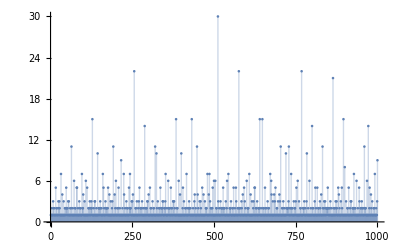

```mathematica
ListPlot[Length@*factorsDivisorD/@Range[1000],PlotRange->All,Filling->Axis]
```

```mathematica
maybeDivisorD=DivisorD;
```

```mathematica
maybeDivisorD[60]
```

5040

```mathematica
definitelyDivisorD[n_Integer]:=
With[{m=maybeDivisorD[n]},
LengthWhile[Range[m],DivisorTau@#≠n&]+1]
```

#### D(8)

```mathematica
{maybeDivisorD[8],definitelyDivisorD[8]}
```

{24,24}

#### D(12)

```mathematica
{maybeDivisorD[12],definitelyDivisorD[12]}
```

{60,60}

#### D(24)

```mathematica
{maybeDivisorD[24],definitelyDivisorD[24]}
```

{360,360}

### Exercise 2.1.22

```mathematica
sumTauSquared[n_]:=
Sum[DivisorTau[k],{k,Divisors[n]}]^2
```

```mathematica
sumTauSquared/@{11,12,13,14}
```

{9,324,9,81}

```mathematica
sumCubedTau[n_]:=
Sum[DivisorTau[k]^3,{k,Divisors[n]}]
```

```mathematica
sumCubedTau/@{11,12,13,14}
```

{9,324,9,81}

```mathematica
sumCubedTau/@Range[100]==sumTauSquared/@Range[100]
```

True

τ( p_1^k_1… p_n^k_n)==(k_1+1) … (k_n+1)

It’s just triangle numbers, right?

```mathematica
n=.
```

```mathematica
DivisorTau[1]
```

1

```mathematica
DivisorTau[{1,2,4}]
```

{1,2,3}

```mathematica
Total[DivisorTau/@Divisors[30]]
```

27

```mathematica
DivisorTau/@{2,3,5}
```

{2,2,2}

For  m== p_1^k_1 …  p_n^k_n, d∣m⇒d==p_1^ℓ_1…  p_n^ℓ_n, where 0≤ℓ_j≤k_j.

("∑")_(d∣m)τ(m)==("∑")_(ℓ_1=0)^k_1("∑")_(ℓ_n=0)^k_nτ(p_1^ℓ_1)τ(p_n^ℓ_n)

This can be rewritten as

∏_(j=1)^n ∑_(l_j=0)^k_j τ(p_j^ℓ_j)

```mathematica
FullSimplify[DivisorSigma[0,p^k],{p∈Primes,k∈Integers,0≤k}]
```

1+k

```mathematica
Sum[(1+l),{l,0,k}]
```

1/2 (1+k) (2+k)

Thus we have

∏_(j=1)^n ((k+1)(k+2))/2

The rest is just a familiar identity between sums.

## Chapter 2.2

```mathematica
FullSimplify[DivisorSigma[0,2^(p-1)],{p∈Integers,1<p}]
```

p

```mathematica
DivisorSigma[16]
```

31

```mathematica
Assuming[p∈Primes,
Refine[p∈Primes]]
```

True

### Exercise 2.2.1

```mathematica
With[{m=3^3,n=2^2},
mt=MultiplicationTable[Divisors[m],Divisors[n]]]
```

| 1 | 2 | 4
1 | 1 | 2 | 4
3 | 3 | 6 | 12
9 | 9 | 18 | 36
27 | 27 | 54 | 108

```mathematica
Total[First@mt,2]
```

280

```mathematica
{Total[2^Range[0,2]],Total[3^Range[0,3]]}
```

{7,40}

### Exercise 2.2.2

If n is a perfect, even number it has the form n==2^(p-1) M_p, where both p and M_p are prime. Then

n==2^(p-1)(2^p-1)==2/2×2^(p-1)(2^p-1)==(2^p(2^p-1))/2

```mathematica
Sum[k,{k,1,2^p-1}]
```

2^(-1+p) (-1+2^p)

## Chapter 2.3

```mathematica
n=.
```

```mathematica
g=.
```

```mathematica
m=.
```

```mathematica
?DivisorSum
```

DivisorSum[n,form] represents the sum of form[i] for all i that divide n.
DivisorSum[n,form,cond] includes only those divisors for which cond[i] gives True.

```mathematica
u[n_]:=1;
```

```mathematica
𝒩[n_]:=n;
```

```mathematica
e[n_Integer]:=KroneckerDelta[n,1];
```

```mathematica
FullSimplify[DirichletConvolve[f[n],g[n],n,m]==DivisorSum[m,f[#]*g[m/#]&],
Assumptions->{m∈Integers,0<m}
]
```

DirichletConvolve[f[n],g[n],n,m]==∑_(n∣m) f[n] g[m/n]

### Exercise 2.3.1

```mathematica
DirichletConvolve[1,1,n,m]
```

DivisorSigma[0,m]

### Exercise 2.3.2

```mathematica
DivisorSum[m,ℯ[#]*f[m/#]&]
```

∑_(n∣m) f[m/n] ℯ[n]

If ℯ(k)==k,1, then only the f(m/1) term in the sum remains.

```mathematica
FunctionExpand[DivisorSum[m,(m/#)*KroneckerDelta[#-1]&],{m∈Integers,0<m}]
```

∑_(n∣m) (m KroneckerDelta[1-n])/n

### Exercise 2.3.3

```mathematica
compare={#,MoebiusMu@#,Total@MoebiusMu@#}&@*Divisors
```

{#1,MoebiusMu[#1],Total[MoebiusMu[#1]]}&@*Divisors

```mathematica
compare[4]
```

{{1,2,4},{1,-1,0},0}

```mathematica
compare[6]
```

{{1,2,3,6},{1,-1,-1,1},0}

```mathematica
compare[10]
```

{{1,2,5,10},{1,-1,-1,1},0}

```mathematica
compare[2]
```

{{1,2},{1,-1},0}

```mathematica
DivisorSum[m,MoebiusMu]
```

KroneckerDelta[1-m]

### Exercise 2.3.4

g==f⋆μ⇒g⋆u==f⋆(μ⋆u)⇒g⋆u==f⋆e⇒f==g⋆u

### Exercise 2.3.5

```mathematica
DirichletConvolve[MoebiusMu[n],DivisorSigma[0,n],n,m]
```

1